### Main functions

```mathematica
importResolutionsFromImage[img_,gridw_,gridh_]:=Map[0.3+(1-If[ListQ@#,First@#,#])*0.7&,ImageData@ImageResize[ColorConvert[img,"GrayScale"],{gridw,gridh}],{2}]
```

```mathematica
(*given a resolution value, create a small graph representing a grid in that resolution*)
createGraphForResolutionCell[resolution_,minNodeName_]:=
Module[{pixels,table,counterFromWH},
counterFromWH[w_,h_,maxw_]:=w+h*maxw;
pixels=Floor[resolution*10];
table=Table[(minNodeName+counterFromWH[w,h,pixels]-1)->(minNodeName+counterFromWH[w+1,h,pixels]-1),{w,pixels-1},{h,pixels}];
table=Join[table,Table[(minNodeName+counterFromWH[w,h,pixels]-1)->(minNodeName+counterFromWH[w,h+1,pixels]-1),{w,pixels},{h,pixels-1}]];
Flatten@table
]
```

```mathematica
(*given a graph like the one built by createGraphForResolutionCell,return a specific side of such graph*)
getSide[grid_,whichSide_]:=
Module[{nums,min,max,w},
nums=Union@Flatten[List@@@grid];
min=Min[nums];
max=Max[nums];
w=Sqrt[1+max-min];
If[whichSide==="Left",Return[min+(w*(#-1))&/@Range[w]]];
If[whichSide==="Right",Return[min+(w*(#-1)+w-1)&/@Range[w]]];
If[whichSide==="Top",Return[Take[nums,w]]];
Take[nums,-w]
]
```

```mathematica
getLeftSide[grid_]:=getSide[grid,"Left"]
```

```mathematica
getRightSide[grid_]:=getSide[grid,"Right"]
```

```mathematica
getTopSide[grid_]:=getSide[grid,"Top"]
```

```mathematica
getBottomSide[grid_]:=getSide[grid,"Bottom"]
```

```mathematica
connectPoints[pointsA_,pointsB_]:=
Module[{pA,pB,dist,pa2,idx,idxpre},
If[Length@pointsA>Length@pointsB,pA=pointsA;pB=pointsB,pB=pointsA;pA=pointsB];
dist=(Length@pB)/(Length@pA);
idx=1;
pa2=#->(idxpre=idx;idx=idx+dist;pB[[Floor[idxpre]]])&/@pA;
pa2
]
```

```mathematica
(*returns {graph,graphgrid},graph is the full graph with interconnectors included, graphgrid is the grid of subgraphs that compose the graph without the connectors*)createGraphFromResolutionGrid[resolutionGrid_]:=
Module[{gridw,gridh,graphgrid,last,minNode,wConnectors,hConnectors,fullgraph},
gridw=Length@resolutionGrid[[1]];
gridh=Length@resolutionGrid;
minNode=0;
graphgrid=Map[(last=createGraphForResolutionCell[#,minNode];
minNode=Max@Flatten[List@@@last];last)&,resolutionGrid,{2}];
wConnectors=Flatten@Table[connectPoints[getRightSide[graphgrid[[h]][[w]]],getLeftSide[graphgrid[[h]][[w+1]]]],{w,gridw-1},{h,gridh}];
hConnectors=Flatten@Table[connectPoints[getBottomSide[graphgrid[[h]][[w]]],getTopSide[graphgrid[[h+1]][[w]]]],{w,gridw},{h,gridh-1}];
fullgraph=Join[Flatten@graphgrid,wConnectors,hConnectors];
{fullgraph,graphgrid}
]
```

```mathematica
squareCellNumToXY[num_,min_,gridw_]:=
{(*x*)Mod[(num-min),gridw],(*y*)Floor[(num-min)/gridw]}
```

```mathematica
squareCellToSpace[grid_,x_,y_,w_,h_,mindist_]:=
Module[{nums,min,max,cellw,numcoord},
nums=Union@Flatten[List@@@grid];
min=Min[nums];
max=Max[nums];
cellw=Sqrt[1+max-min];(*cells are square*)
numcoord=#->squareCellNumToXY[#,min,cellw]&/@nums;
numcoord=#[[1]]->{x+mindist+(w-2 mindist) #[[2,1]]/(cellw-1),y+mindist+(h-2 mindist) #[[2,2]]/(cellw-1)}&/@numcoord;
numcoord
]
```

```mathematica
(*generate coordinates for all vertices of a megagrid generated by createGraphFromResolutionGrid (it's called megagrid because it's a grid of grids)*)
computeXYForFullMegaGrid[graphgrid_,x_,y_,w_,h_,mindist_]:=
Module[{gridsxy,gridw,gridh,graphxy,maxy},
gridw=Length@graphgrid[[1]];
gridh=Length@graphgrid;
gridsxy=MapIndexed[squareCellToSpace[#,x+#2[[2]]*w/gridw,y+#2[[1]]*h/gridh,w/gridw,h/gridh,mindist]&,graphgrid,{2}];
graphxy=Flatten@gridsxy;
maxy=Max[#[[2,2]]&/@Flatten[graphxy]];
graphxy=#[[1]]->{#[[2,1]],maxy-#[[2,2]]}&/@graphxy;(*invert y coordinate*)
graphxy
]
```

```mathematica
(*generates a maze from any kind of graph
maxdepth is the maximum depth for the dfs algorithm; it can be infinity for small images, bigger images need an integer value; if maxdeep is too small some parts of the images will be white*)
generateMazeFromGraph[graph_,entrance_,exit_,maxdeep_:Infinity]:=
Module[{generateMazeFromCell,visited,lim,maze},
generateMazeFromCell[parent_,cell_,maxdeepvalue_]:=
Module[{neighbours,newgraphs={},newgraphs2={}},
If[MemberQ[visited,cell],Return@{}];
If[maxdeepvalue==0,Return@{}];
If[parent=!=None,AppendTo[newgraphs,parent->cell]];
visited=AppendTo[visited,cell];
neighbours=Complement[Union@Flatten[List@@@Select[graph,#[[1]]==cell||#[[2]]==cell&]],visited];
(*neighbours=RandomSample[neighbours,Ceiling[Random[]*Length@neighbours]];*)
neighbours=RandomSample[neighbours];
If[!MemberQ[visited,#],
AppendTo[newgraphs2,generateMazeFromCell[cell,#,maxdeepvalue-1]]]&/@neighbours;
Flatten@Append[newgraphs2,newgraphs]
];
visited={};
lim=$RecursionLimit;
$RecursionLimit=Infinity;
maze=generateMazeFromCell[None,entrance,maxdeep];
$RecursionLimit=lim;
maze
]
```

```mathematica
generateMazeFromImage[img_,resolutionX_,resolutionY_,maxPathLength_:Infinity,showBackgroundGrids_: False,showBackgroundGridsOnly_:False]:=
Module[{entrance,exit,resolutions,fullgraph,graphgrid,graphxy,fullgraph2,maze,mazegfx,graphic},
resolutions=importResolutionsFromImage[img,resolutionX,resolutionY];
{fullgraph,graphgrid}=createGraphFromResolutionGrid[resolutions];
graphxy=computeXYForFullMegaGrid[graphgrid,0,0,10 resolutionX,10 resolutionY,1];
entrance=Min@Flatten[List@@@fullgraph];
exit=Max@Flatten[List@@@fullgraph];
If[!showBackgroundGridsOnly,
maze=generateMazeFromGraph[fullgraph,entrance,exit,maxPathLength];
maze=Rule@@@(Sort/@List@@@maze);(*sort*)
mazegfx=ReplaceAll[Line[{#[[1]],#[[2]]}]&/@maze,graphxy];
];
fullgraph=Rule@@@(Sort/@List@@@fullgraph);(*sort*)
fullgraph2=If[showBackgroundGrids||showBackgroundGridsOnly,fullgraph,{}];
fullgraph2=ReplaceAll[Line[{#[[1]],#[[2]]}]&/@fullgraph2,graphxy];
If[!showBackgroundGridsOnly,
fullgraph2=Complement[fullgraph2,mazegfx];
graphic=Join[{Gray,AbsoluteThickness[3],fullgraph2},{Black,AbsoluteThickness[5],mazegfx},{Green,Disk[entrance/.graphxy]},{Red,Disk[exit/.graphxy]}];
,
graphic={Black,AbsoluteThickness[5],fullgraph2};
];
Graphics[graphic,ImageSize->resolutionX*1500/16]
]
```

### Generate a big test maze

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*img by Larry Ewing, see  http://www.isc.tamu.edu/~lewing/linux/ for details*)
```

```mathematica
img=ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/sketches/candles.jpg"],200];
```

```mathematica
{resx,resy}=ImageDimensions@img
```

{200,309}

```mathematica
resx2=Round[resx/10];
resy2=Round[resy/10];
{resx2,resy2}
```

{20,31}

```mathematica
ImageResize[ColorConvert[img,"GrayScale"],{resx2,resy2}]
```

-Graphics-

```mathematica
ColorNegate@ColorConvert[img,"GrayScale"]
```

-Graphics-

```mathematica
gfx=generateMazeFromImage[img,resx2,resy2,3000];
```

```mathematica
gfx>>"/home/russellfoltzsmith/Documents/art/themaze/data/candlemaze.m";
```

```mathematica
imggfx=Image[gfx];
```

```mathematica
Export["/home/russellfoltzsmith/Documents/art/themaze/data/mazebig.jpg",imggfx];
```

```mathematica
smallimg=ImageResize[imggfx,400]
```

-Graphics-

```mathematica
ImageDimensions@imggfx-40
```

{1835,2642}

```mathematica
ImageCrop[imggfx,ImageDimensions@imggfx-80]
```

-Graphics-

```mathematica
w=ColorNegate[Image[WatershedComponents[ImageCrop[imggfx,ImageDimensions@imggfx-110]],"Bit"]];
HighlightImage[ImageCrop[imggfx,ImageDimensions@imggfx-80],Dilation[w,1]]
```

-Graphics-

```mathematica
Blend[{ImageCrop[imggfx,ImageDimensions@imggfx-80],Import["/home/russellfoltzsmith/Documents/art/themaze/queencrop.png"]},.3]
```

-Graphics-

```mathematica
Export["data/mazesmall.jpg",smallimg];
```

```mathematica
ImageResize[imggfx,resx2*4]
```

-Graphics-

```mathematica
ImageResize[imggfx,resx2]
```

-Graphics-

### Sample images for article

#### small resolution tux

```mathematica
resx3=Round[resx/40];
resy3=Round[resy/40];
{resx3,resy3}
```

{6,8}

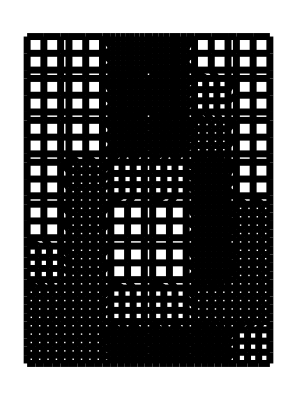

```mathematica
generateMazeFromImage[img,resx3,resy3,Infinity,True,True]
```

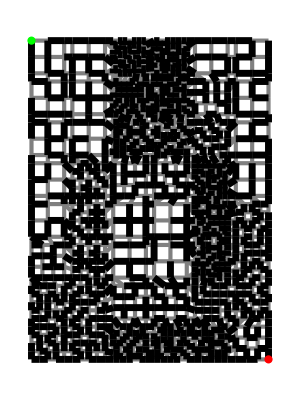

```mathematica
generateMazeFromImage[img,resx3,resy3,300,True]
```

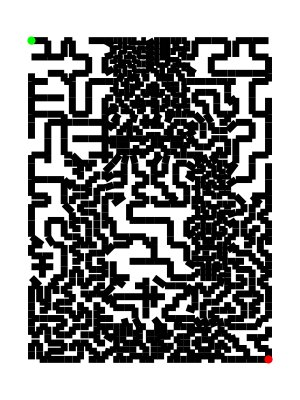

```mathematica
generateMazeFromImage[img,resx3,resy3,350]
```

#### lattice examples

```mathematica
resolutions={{1,1},{1,1}}
```

{{1,1},{1,1}}

```mathematica
(*todo: rewrite so that no code from generateMazeFromImage is repeated (maybe add as parameter to generateMazeFromImage)*)
generateGraphicFromResolutionGrid[resolutionGrid_,showConnections_:True]:=
Module[{fullgraph,graphgrid,fullgraph2,graphxy,graphic,gridw,gridh},
{fullgraph,graphgrid}=createGraphFromResolutionGrid[resolutionGrid];
gridw=Length@resolutionGrid[[1]];
gridh=Length@resolutionGrid;
graphxy=computeXYForFullMegaGrid[graphgrid,0,0,10 gridw,10gridh,1];
If[showConnections,
fullgraph=Rule@@@(Sort/@List@@@fullgraph);(*sort*)
fullgraph2=ReplaceAll[Line[{#[[1]],#[[2]]}]&/@fullgraph,graphxy];
,
fullgraph=Rule@@@(Sort/@List@@@Flatten@graphgrid);(*sort*)
fullgraph2=ReplaceAll[Line[{#[[1]],#[[2]]}]&/@fullgraph,graphxy];
];
graphic={Gray,AbsoluteThickness[3],fullgraph2};
graphic={Black,AbsoluteThickness[5],fullgraph2};
Graphics[graphic,ImageSize->400]
]
```

```mathematica
generateGraphicFromResolutionGrid@{{0.3,0.3},{0.3,0.3}};
```

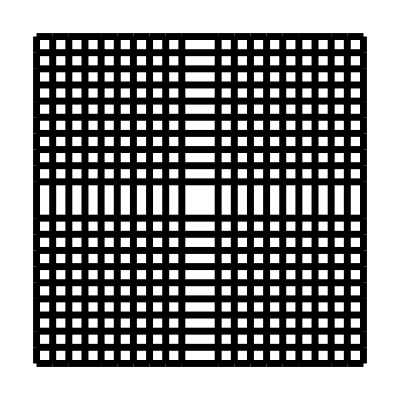

```mathematica
generateGraphicFromResolutionGrid@{{1,1},{1,1}}
```

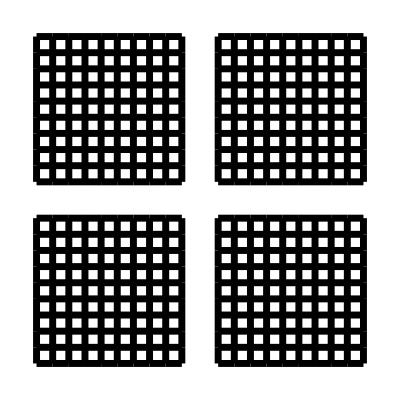

```mathematica
generateGraphicFromResolutionGrid[{{1,1},{1,1}},False]
```

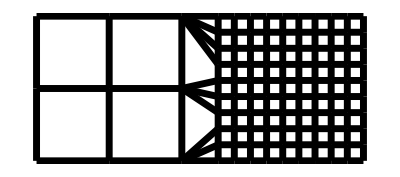

```mathematica
generateGraphicFromResolutionGrid@{{0.3,1}}
```

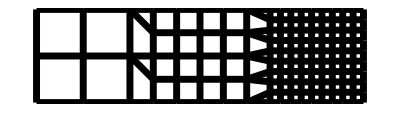

```mathematica
generateGraphicFromResolutionGrid@{{0.3,0.5,1}}
```

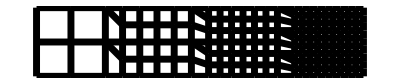

```mathematica
generateGraphicFromResolutionGrid@{{0.3,0.5,0.7,1}}
```

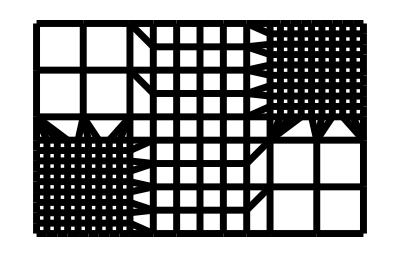

```mathematica
generateGraphicFromResolutionGrid@{{0.3,0.5,1},{1,0.5,0.3}}
```

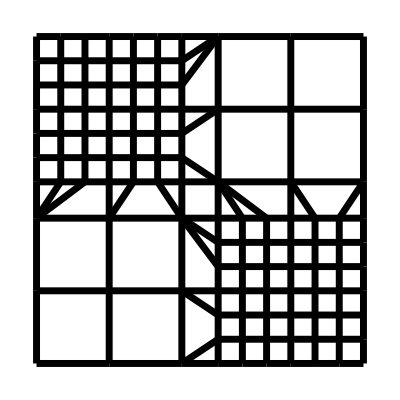

```mathematica
generateGraphicFromResolutionGrid@{{0.7,0.3},{0.3,0.7}}
```

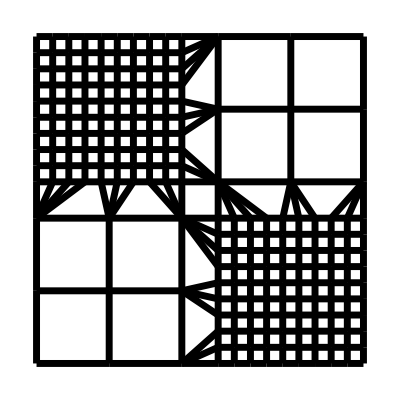

```mathematica
generateGraphicFromResolutionGrid@{{1,0.3},{0.3,1}}
```

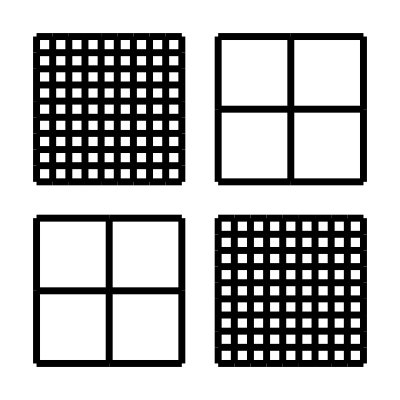

```mathematica
generateGraphicFromResolutionGrid[{{1,0.3},{0.3,1}},False]
```